```mathematica
(* Set Directory to Extract and Save Files to *)
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6"]
Import["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Oscillator Configurations.png"]
```

C:\Users\physk\OneDrive\Desktop\Hidden Quantum Network N_6

-Graphics-

```mathematica
(* Colors *)
redcolor=RGBColor[246/255,0/255, 0/255];
greencolor=RGBColor[108/255,166/255, 70/255];
bluecolor=RGBColor[0/255, 129/255, 204/255];
yellowcolor=RGBColor[255/255,200/255, 31/255];
Row[{redcolor, greencolor, bluecolor, yellowcolor}]
```

RGBColor[Rational[82, 85], 0, 0]RGBColor[Rational[36, 85], Rational[166, 255], Rational[14, 51]]RGBColor[0, Rational[43, 85], Rational[4, 5]]RGBColor[1, Rational[40, 51], Rational[31, 255]]

```mathematica
(* Plot Formatting *)
length=400; width=400;
PlotFormat={Joined->True, PlotRange-> {0, 3}, ImageSize->{length, width}, AspectRatio->width/length, LabelStyle->Directive[Black, 25], AxesLabel->{"  τ", "𝒩"}, AxesStyle->Directive[Black,23], BaseStyle->{FontFamily->"Latin Modern Roman"}};
```

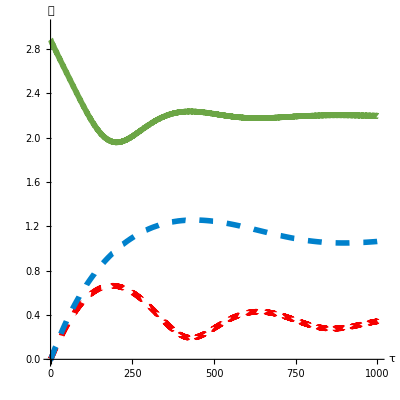
-Graphics--Graphics-

```mathematica
(* Get Data for Entanglement Network Configuration 2 *)
Config2Data=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config2\\Entanglement Resonance Omega = 4, omega12 = 2, omega34 = 3, omega56 = 5.txt"];
Config2Pic=Import["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config2\\Config2.png"];
(* Plot *)
Config2Plot=ListPlot[Config2Data, Evaluate[PlotFormat], PlotStyle->{Directive[Thickness[0.01], redcolor, Dashing[0.025]], Directive[Thickness[0.01], greencolor], Directive[Thickness[0.01], bluecolor, Dashing[0.025]]}];
Row[{Config2Plot, Image[Config2Pic, Magnification->1]}]
ConfigurationA1=Config2Plot;
```

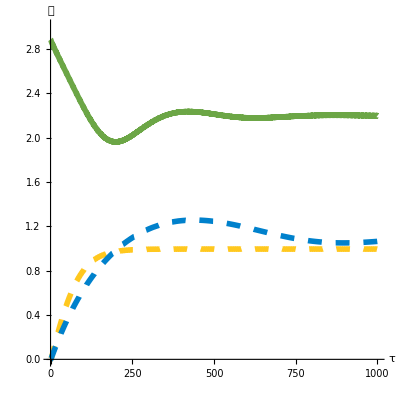
-Graphics--Graphics-

```mathematica
(* Get Data for Entanglement Network Configuration 6 *)
Config6Data=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config6\\Entanglement Resonance Omega = omega12 = 4, omega34 = 3, omega56 = 5.txt"];
Config6Pic=Import["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config6\\Config6.png"];
(* Plot *)
Config6Plot=ListPlot[Config6Data, Evaluate[PlotFormat], PlotStyle->{Directive[Thickness[0.01], yellowcolor, Dashing[0.025]], Directive[Thickness[0.01], greencolor], Directive[Thickness[0.01], bluecolor, Dashing[0.025]]}];
Row[{Config6Plot, Image[Config6Pic, Magnification->1]}]
ConfigurationA2=Config6Plot;
```

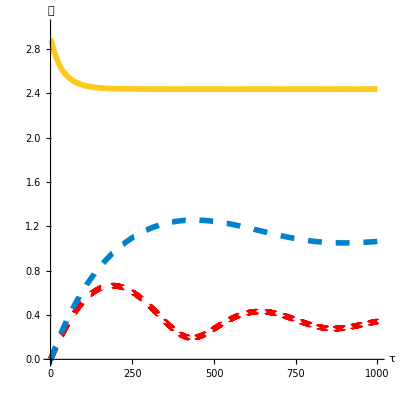
-Graphics--Graphics-

```mathematica
(* Get Data for Entanglement Network Configuration 10 *)
Config10Data=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config10\\Entanglement Resonance Omega = omega34 = 4, omega12 = 2, omega56 = 5.txt"];
Config10Pic=Import["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config10\\Config10.png"];
(* Plot *)
Config10Plot=ListPlot[Config10Data, Evaluate[PlotFormat], PlotStyle->{Directive[Thickness[0.01], redcolor, Dashing[0.025]], Directive[Thickness[0.01], yellowcolor], Directive[Thickness[0.01], bluecolor, Dashing[0.025]]}];
Row[{Config10Plot, Image[Config10Pic, Magnification->1]}]
ConfigurationA3=Config10Plot;
```

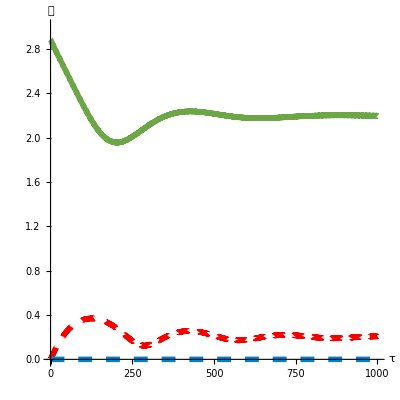
-Graphics--Graphics-

```mathematica
(* Get Data for Entanglement Network Configuration 3 *)
Config3Data=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config3\\Entanglement Resonance Ω = 4, omega125 = 2, omega34 = 3, omega6 = 5.txt"];
Config3Pic=Import["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config3\\Config3.png"];
(* Plot *)
Config3Plot=ListPlot[Config3Data, Evaluate[PlotFormat], PlotStyle->{Directive[Thickness[0.01], redcolor, Dashing[0.025]], Directive[Thickness[0.01], greencolor], Directive[Thickness[0.01], bluecolor, Dashing[0.025]]}];
Row[{Config3Plot, Image[Config3Pic, Magnification->1]}]
ConfigurationB1=Config3Plot;
```

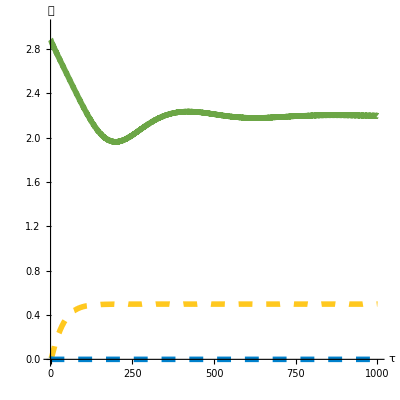
-Graphics--Graphics-

```mathematica
(* Get Data for Entanglement Network Configuration 7 *)
Config7Data=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config7\\Entanglement Resonance Ω = omega125 = 4, omega34 = 3, omega6 = 5.txt"];
Config7Pic=Import["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config7\\Config7.png"];
(* Plot *)
Config7Plot=ListPlot[Config7Data, Evaluate[PlotFormat], PlotStyle->{Directive[Thickness[0.01], yellowcolor, Dashing[0.025]], Directive[Thickness[0.01], greencolor], Directive[Thickness[0.01], bluecolor, Dashing[0.025]]}];
Row[{Config7Plot, Image[Config7Pic, Magnification->1]}]
ConfigurationB2=Config7Plot;
```

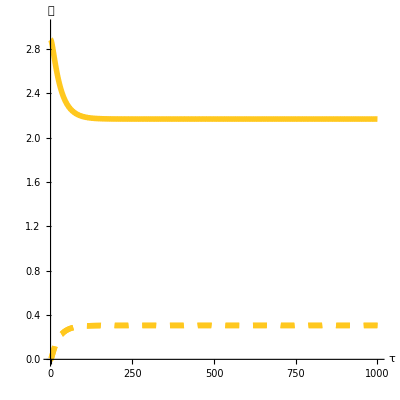
-Graphics--Graphics-

```mathematica
(* Get Data for Entanglement Network Configuration 16 *)
Config16Data=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config16\\Entanglement Resonance Omega = omega12 = omega34 = omega56 = 4.txt"];
Config16Pic=Import["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6\\Config16\\Config16.png"];
(* Plot *)
Config16Plot=ListPlot[Config16Data, Evaluate[PlotFormat], PlotStyle->{Directive[Thickness[0.01], yellowcolor, Dashing[0.025]], Directive[Thickness[0.01], yellowcolor], Directive[Thickness[0.01], yellowcolor, Dashing[0.025]]}];
Row[{Config16Plot, Image[Config16Pic, Magnification->1]}]
ConfigurationC1=Config16Plot;
```

```mathematica
(* Set Directory to Extract and Save Files to *)
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Hidden Quantum Network N_6"];

HiddenQuantumNetworkConfigurations=Rasterize[GraphicsGrid[{{ConfigurationA1, ConfigurationA2, ConfigurationA3}, {ConfigurationB1, ConfigurationB2, ConfigurationC1}}, ImageSize->{1500, 1000}, AspectRatio->Full]]
Export["HiddenQuantumNetworkConfigurations.png", HiddenQuantumNetworkConfigurations]
```

-Graphics-

HiddenQuantumNetworkConfigurations.png